## (See end for Project 1 VPA calculations) Scattering from a Spherical Square Well

## Preliminaries

In this notebook, we compute the phase shifts of the potential with V = -V0 for r<R and V=0 for r>R with an analytic formula and using the Variable Phase Approach (VPA). The reduced mass is μ.

Work in units where ℏ=1 and we measure mass in units of μ and lengths in terms of R.  Thus we set μ and R to 1. However, we will continue to make them explicit in the formulas.

```mathematica
μ = 1; R=1.;
```

The only parameter to adjust now is the depth V0.

```mathematica
Vsw[r_,V0_] := -V0 HeavisideTheta[R-r]  (* Define the square well *)
```

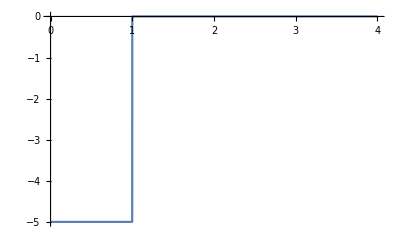

```mathematica
Plot[Vsw[r,5],{r,0,4},Exclusions->None]  (* Uncomment to check potential *)
```

```mathematica
Ek[k_] := k^2/(2μ)   (* Convenient definition of kinetic energy *)
```

## Analytic result for the phase shift

Use the formula for δ(E) from one of the problems, converting it to δ(k) using Ek(k):

```mathematica
deltaAnalytic[k_,V0_] := ArcTan[Sqrt[Ek[k]/(Ek[k]+V0)] Tan[R Sqrt[2μ(Ek[k]+V0)]]]-R Sqrt[2 μ Ek[k]]
```

Use Cell->Convert  to->TraditionalForm to get it in a form easier to check we have entered it correctly:
deltaAnalytic(k_,V0_):=tan^-1(√((Ek(k))/(Ek(k)+V0)) tan(R √(2 μ (Ek(k)+V0))))-R √(2 μ Ek(k))

Always check that the function actually produces a number.

```mathematica
deltaAnalytic[5,0.5]
```

-6.17727

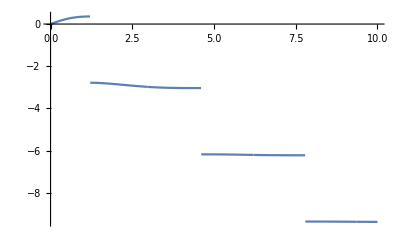

```mathematica
Plot[deltaAnalytic[k,0.5],{k,0,10}]
```

What is going on with the steps?  Why are they there?  Is the phase shift really discontinuous?  How would you fix it?

Here is one “fix” that makes the result continuous for this example, but we will still have issues when V0 is large enough to support bound states.

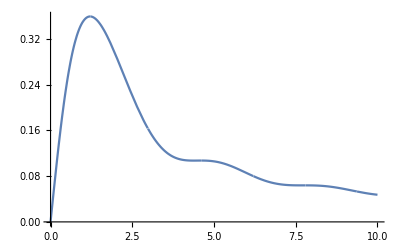

```mathematica
Plot[ArcTan[Tan[deltaAnalytic[k,0.5]]],{k,0,10}]
```

```mathematica
deltaAnalyticAdjusted[k_,V0_] := ArcTan[Tan[deltaAnalytic[k,V0]]]
```

We can also avoid this issue by looking at k Cot[δ(k)] instead, which doesn’t have these ambiguities.

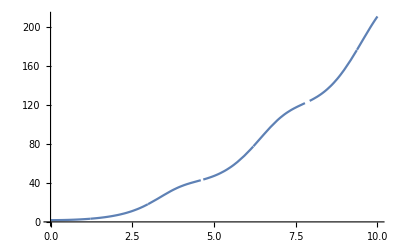

```mathematica
Plot[k Cot[deltaAnalytic[k,0.5]],{k,0,10}]
```

## Phase shift from the Variable Phase Approach

Use the formula: deltarho'(r)==-(2 μ Vsw(r) sin^2(deltarho(r)+k r))/k with the initial condition that deltarho(0) = 0.

We’ll need a numerical differential equation solver.  In Mathematica this is NDSolve:

```mathematica
?NDSolve
```

In principle we integrate out to infinity.  In practice, we choose a value of k and integrate out to Rmax, chosen to be well beyond the range of the potential (at which point the right side of the equation for deltarho’(r) is zero), and then evaluate deltarho(Rmax), which is the phase shift for momentum k.  Here is an implementation:

```mathematica
deltaVPA[k_,V0_] :=(
Rmax = 10; (* integrate out to Rmax; just need Rmax > R for square well *)ans = NDSolve[{deltarho'[r]==-(1/k)2μ Vsw[r,V0] Sin[k r + deltarho[r]]^2,deltarho[0]==0},deltarho,{r,0,Rmax},AccuracyGoal->6,PrecisionGoal->6];
(deltarho[r] /. ans)[[1]] /. r->Rmax  (* evaluate at r=Rmax *)
)
```

Do a quick check against the analytic result with sample values for k and V0 to see the accuracy we are getting (we use NumberForm to get 10 digits displayed):

```mathematica
NumberForm[ deltaVPA[2,.5],10]
```

0.2908784316

```mathematica
NumberForm[ deltaAnalyticAdjusted[2,.5], 10]
```

0.2908679106

Does it work?  Check a few more values to be sure.

To get more digits correct, increase AccuracyGoal and PrecisionGoal (at the cost of slower evaluation of the function).

Check the cutoff phase shift out to Rmax.  Does this plot make sense?

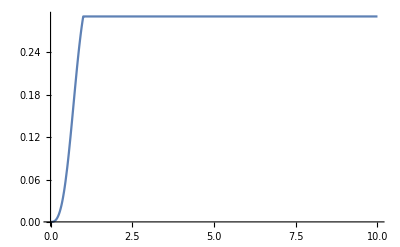

```mathematica
Plot[Evaluate[deltarho[r]/.ans],{r,0,Rmax}]
```

Now that it seems to be working, try plots of the k Cot[δ] and δ for two different depths.  How do you explain the results in terms of Levinson’s theorem?

```mathematica
V0 = 1.;
```

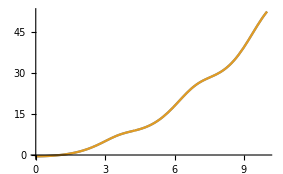

```mathematica
Plot[{k Cot[deltaAnalytic[k,V0]],k Cot[deltaVPA[k,V0]]},{k,0,10},PlotRange->Full]  (* Check that both plots are really here! *)
```

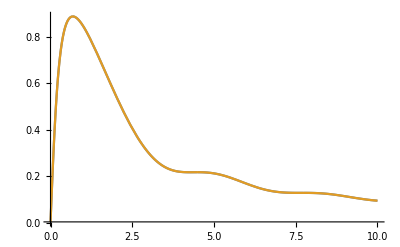

```mathematica
Plot[{deltaAnalyticAdjusted[k,V0],deltaVPA[k,V0]},{k,0.001,10},PlotRange->Full]
```

```mathematica
V0 = 2.;
```

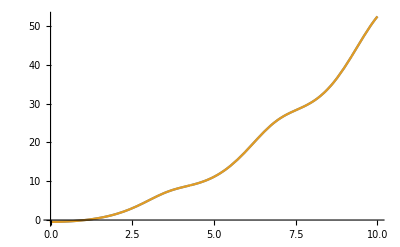

```mathematica
Plot[{k Cot[deltaAnalytic[k,V0]],k Cot[deltaVPA[k,V0]]},{k,0,10},PlotRange->Full]  (* Check that both plots are really here! *)
```

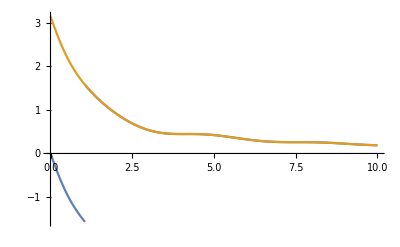

```mathematica
Plot[{deltaAnalyticAdjusted[k,V0],deltaVPA[k,V0]},{k,0.001,10},PlotRange->Full]
```

## Now it’s time to play!

Check whether Levinson’s theorem holds by calculating phase shifts for increasing depths V0 and noting the jump to δ(0) = nπ, where n is the number of bound states (found, for example, from the square_well_example.nb notebook).

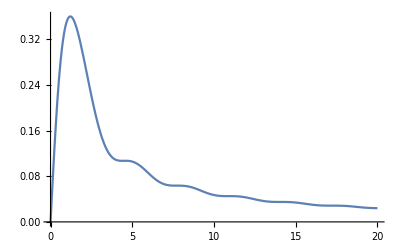
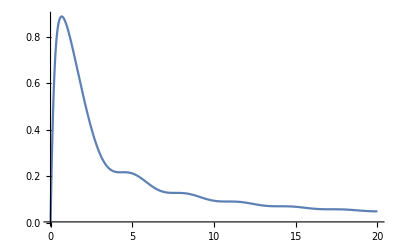
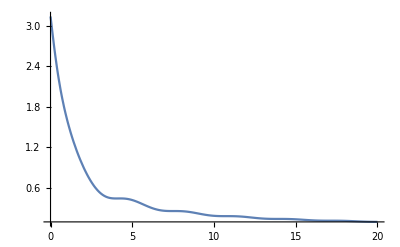
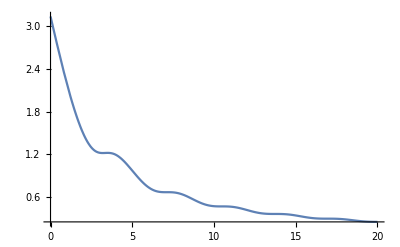
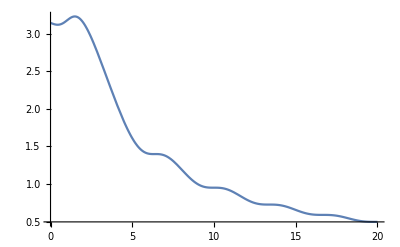
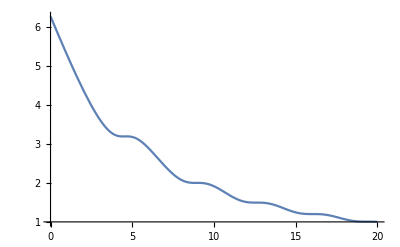

```mathematica
Table[Plot[{deltaVPA[k,V0]},{k,0.001,20},PlotRange->Full],{V0,{0.5,1.0,2.0,5.0,10.0,20.0}}] (* Try for V0 = 0.5 to 20 *)
```

Does it work?  [Note: we start at k=0.001 to avoid numerical issues at k=0.]

This is really fun using Manipulate!

```mathematica
Manipulate[Plot[deltaVPA[k,V0],{k,0.001,10},PlotRange->Full],{V0,0,20,Appearance->"Labeled"}]
```

Verify that the threshold bound state appears at the V0 corresponding to the jump in δ(0).
Check that these two formulas are correct:

```mathematica
1/(2μ)(Pi/(2R))^2 //N  (* Value of V0 for a single bound state at E=0 *)
```

1.2337

```mathematica
1/(2μ)(3Pi/(2R))^2 //N  (* Value of V0 for two bound states at E=0 *)
```

11.1033

Check that k Cot[δ] behaves as expected (and Cot[δ] close to a zero-energy bound state):

```mathematica
Manipulate[Plot[k Cot[deltaVPA[k,V0]],{k,0.001,.2},PlotRange->Full],{V0,0,20,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[ Cot[deltaVPA[k,V0]],{k,0.001,.2},PlotRange->Full],{V0,0,20,Appearance->"Labeled"}]
```

## Other potentials . . .

Add a short-range repulsive square well:

```mathematica
Vdoublesw[r_,V0_, Vc_,Rc_] := (Vc+V0) HeavisideTheta[Rc-r]-V0 HeavisideTheta[R-r]  (* Define the square well *)
```

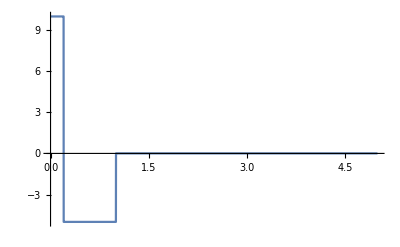

```mathematica
Plot[Vdoublesw[r,5,10,.2],{r,0,5},Exclusions->None]
```

```mathematica
deltaVPAdoublesw[k_,V0_, Vc_,Rc_] :=(
Rmax = 10; (* integrate out to Rmax; just need Rmax > R for square well *)ans = NDSolve[{deltarho'[r]==-(1/k)2μ Vdoublesw[r,V0 ,Vc,Rc] Sin[k r + deltarho[r]]^2,deltarho[0]==0},deltarho,{r,0,Rmax}];
(deltarho[r] /. ans)[[1]] /. r->Rmax 
)
```

```mathematica
Manipulate[Plot[deltaVPAdoublesw[k,V0,Vc,Rc],{k,0.001,10},PlotRange->{-Pi,Pi}],{{V0,5},0,20,Appearance->"Labeled"},{{Vc,0},0,100,Appearance->"Labeled"},{{Rc,.2},0,20,Appearance->"Labeled"}]
```

Start with the repulsive well at zero height and then see what happens when you increase it (go up to 100 eventually).

## Project 1

```mathematica
(* export plot to show VPA is same as matrix inversion code for square well *)
```

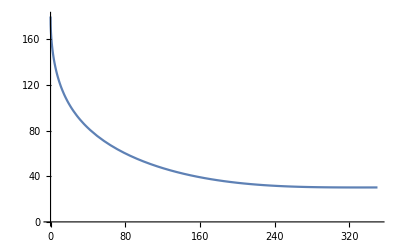

```mathematica
Plot[deltaVPA2[Sqrt[En/83],50,0.01*197]*180/Pi,{En,0,350},PlotRange->{0,180}]
```

```mathematica
Export["VPA phase shifts square well.xlsx", Table[{En,deltaVPA2[Sqrt[En/83],50,0.01*197]*180/Pi},{En,0.00001,350,0.01}]]
```

VPA phase shifts square well.xlsx

## NN potential from Part A using VPA

```mathematica
(* Potential in MeV *)
Va = -10.463;
Vb = -1650.6;
Vc = 6484.3;
a = 1;
b = 4;
c = 7;
μfm = 0.7; (* pion mass in 1/fm*)
MMeV = 938/2; (* approx reduced mass of np system in MeV/c^2*)
(* r is in fm and k is in 1/fm *)
```

```mathematica
(* Define parameterized np potential for singlet S-state with truncation for r beyond ρ *)
```

```mathematica
VtripleYukawa[r_,ρ_] := (Va*Exp[-a*μfm*r]/(μfm*r) + Vb*Exp[-b*μfm*r]/(μfm*r) + Vc*Exp[-c*μfm*r]/(μfm*r))*HeavisideTheta[ρ-r]  

(* Numerical problems with potential blowing up at r=0 so move initial condition slightly *)
(* 2M/k term is 2Mc^2/((hbar*c)^2)k *)
deltaVtripleYukawa [k_,ρ_] := (
Rmax = 10;
ans = NDSolve[{deltarho'[r]==-(1/(197^2*k))*2*MMeV*VtripleYukawa[r,ρ]*Sin[k r + deltarho[r]]^2,deltarho[0.0000000000001]==0},deltarho,{r,0.0000000000001,Rmax}];
(deltarho[r] /. ans)[[1]] /. r->Rmax 
)

EkMeV[k_] := (197*k)^2/(2*MMeV) (* cm frame *)
ElMeV[k_]:=83*k^2 (* lab frame *)
ElMeV[2]
```

332

```mathematica
deltaVtripleYukawa[Sqrt[100/83],20]*180/Pi (* lsesolver gives 24.3483 deg using 50 mesh points for 100 MeV lab frame energy *)
```

24.3675

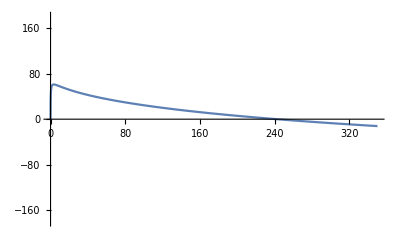

```mathematica
Plot[deltaVtripleYukawa[Sqrt[En/83],20]*180/Pi,{En,0,350},PlotRange->{-180,180}]
```

```mathematica
Export["VPA phase shifts all.xlsx", Table[{En,deltaVtripleYukawa[Sqrt[En/83],20]*180/Pi},{En,0.0000001,350,0.01}]]
```

VPA phase shifts all.xlsx

```mathematica
Manipulate[Plot[deltaVtripleYukawa[Sqrt[En/83],ρ]*180/Pi,{En,0,300},PlotRange->{-180,180}],{{ρ,5},0,20,Appearance->"Labeled"}] (* check convergence with ρ *)
```

## Adjust strength of longest ranged component of NN potential to produce bound state

```mathematica
VtripleYukawa2[r_,ρ_,Vaa_] := (Vaa*Exp[-a*μfm*r]/(μfm*r) + Vb*Exp[-b*μfm*r]/(μfm*r) + Vc*Exp[-c*μfm*r]/(μfm*r))*HeavisideTheta[ρ-r]  

(* Numerical problems with potential blowing up at r=0 so move initial condition slightly *)
(* 2M/k term is 2Mc^2/((hbar*c)^2)k *)
deltaVtripleYukawa2 [k_,ρ_,Vaa_] := (
Rmax = 10;
ans = NDSolve[{deltarho'[r]==-(1/(197^2*k))*2*MMeV*VtripleYukawa2[r,ρ,Vaa]*Sin[k r + deltarho[r]]^2,deltarho[0.0000000000001]==0},deltarho,{r,0.0000000000001,Rmax}];
(deltarho[r] /. ans)[[1]] /. r->Rmax 
)

deltaVtripleYukawa2[0.0001,20,-14.7]
```

3.04274

```mathematica
Manipulate[Plot[deltaVtripleYukawa2[Sqrt[En/83],ρ,Vaa],{En,0,0.0001},PlotRange->{-Pi,Pi}],{{ρ,5},0,20,Appearance->"Labeled"},{{Vaa,-20},-20,-10,Appearance->"Labeled"}]
```

## Effective Range Expansion for NN potential and Square Well Potential

```mathematica
(* solve for coefficients of effective range expansion for NN potential *)
(* kcotδ = -1/a0 + (1/2)r0*k^2 ; valid for k->0 so use small k *)
```

```mathematica
Solve[{-1/a0 + (1/2)*r0*0.0001^2, -1/a0 + (1/2)*r0*0.0002^2}=={0.0001*Cot[deltaVtripleYukawa[0.0001,20]],0.0002*Cot[deltaVtripleYukawa[0.0002,20]]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a0→-17.6219,r0→-2437.15}}

```mathematica
(* check stability with choice of k *)
```

```mathematica
Solve[{-1/a0 + (1/2)*r0*0.001^2, -1/a0 + (1/2)*r0*0.002^2}=={0.001*Cot[deltaVtripleYukawa[0.001,20]],0.002*Cot[deltaVtripleYukawa[0.002,20]]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a0→-17.6464,r0→5.41696}}

```mathematica
Solve[{-1/a0 + (1/2)*r0*0.01^2, -1/a0 + (1/2)*r0*0.02^2}=={0.01*Cot[deltaVtripleYukawa[0.01,20]],0.02*Cot[deltaVtripleYukawa[0.02,20]]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a0→-17.6442,r0→2.77358}}

```mathematica
Solve[{-1/a0 + (1/2)*r0*0.1^2, -1/a0 + (1/2)*r0*0.2^2}=={0.1*Cot[deltaVtripleYukawa[0.1,20]],0.2*Cot[deltaVtripleYukawa[0.2,20]]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a0→-17.6045,r0→2.74733}}

```mathematica
Solve[{-1/a0 + (1/2)*r0*1^2, -1/a0 + (1/2)*r0*2^2}=={1*Cot[deltaVtripleYukawa[1,20]],2*Cot[deltaVtripleYukawa[2,20]]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a0→-0.163914,r0→-8.53568}}

```mathematica
(* coefficient for k^2 term varies a lot since -1/a0 is by far the dominant term for very small k; will use a0 = -17.6442 fm and r0 = 2.77358 fm below since a0 is supposed to be large and negative (almost have bound state) and r0 is expected to be on the order of the nuclear size *)
```

```mathematica
Vsw2[r_,V0_,R_] := -V0 HeavisideTheta[R-r]  (* Define the square well *)
deltaVPA2[k_,V0_,R_] :=(
Rmax = 10; (* integrate out to Rmax; just need Rmax > R for square well *)ans = NDSolve[{deltarho'[r]==-(1/(197^2*k))*2MMeV*Vsw2[r,V0,R] Sin[k r + deltarho[r]]^2,deltarho[0]==0},deltarho,{r,0,Rmax}];
(deltarho[r] /. ans)[[1]] /. r->Rmax  (* evaluate at r=Rmax *)
)
```

```mathematica
Solve[{-1/a0 + (1/2)*r0*0.01^2, -1/a0 + (1/2)*r0*0.02^2}=={0.01*Cot[deltaVPA2[0.01,13.2791,2.6193]],0.02*Cot[deltaVPA2[0.02,13.2791,2.6193]]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a0→-17.6437,r0→2.77353}}

```mathematica
(* using V0 = 13.2791 MeV and R = 2.6193 fm for the square well reproduces the values of a0 and r0 found using the NN potential; there is not a unique potential that gives these values of a0 and r0 *)
```